```mathematica
T = 1/2 m v^2 /. v^2 -> x' [t]^2+y'[t]^2+ ((nx[x[t],y[t]]x'[t] + ny[x[t],y[t]] y'[t])/nz[x[t],y[t]])^2
T = 1/2 m v^2 /. v^2 -> x' [t]^2+y'[t]^2
```

1/2 m (x'[t]^2+y'[t]^2+(nx[x[t],y[t]] x'[t]+ny[x[t],y[t]] y'[t])^2/nz[x[t],y[t]]^2)

1/2 m (x'[t]^2+y'[t]^2)

```mathematica
V = m g h[x[t],y[t]]
```

m (gx x[t]+gy y[t])

```mathematica
L = T-V
L = L /. {nx[x[t],y[t]]->-D[h[x[t],y[t]],x[t]],ny[x[t],y[t]]->-D[h[x[t],y[t]],y[t]],nz[x[t],y[t]]->1};
L
```

-m (gx x[t]+gy y[t])+1/2 m (x'[t]^2+y'[t]^2)

-m (gx x[t]+gy y[t])+1/2 m (x'[t]^2+y'[t]^2)

```mathematica
eq1 = D[D[L,x'[t]],t]==D[L,x[t]] // Simplify
eq2 = D[D[L,y'[t]],t]==D[L,y[t]] // Simplify
```

m (gx+x''[t])==0

m (gy+y''[t])==0

```mathematica
Clear[h,g]
Solve[{eq1,eq2},{x''[t],y''[t]}]
```

{{x''[t]→-gx,y''[t]→-gy}}

```mathematica
h[x_,y_] =gx x + gy y
g = 1
```

gx x+gy y

1

```mathematica
eqs = {eq1,eq2}
```

{m (gx+x''[t])==0,m (gy+y''[t])==0}

```mathematica
sol = DSolveValue[eqs,{x[t],y[t]},{t}]
```

{-(gx t^2)/2+C[1]+t C[2],-(gy t^2)/2+C[3]+t C[4]}

```mathematica
Csol = Solve[{sol[[1]] ==x0,D[sol[[1]],t] ==vx0,sol[[2]] ==y0,D[sol[[2]],t] ==vy0} /. t->0,{C[1],C[2],C[3],C[4]}][[1]]
sol /. Csol // Simplify
```

{C[1]→x0,C[2]→vx0,C[3]→y0,C[4]→vy0}

{-(gx t^2)/2+t vx0+x0,-(gy t^2)/2+t vy0+y0}

```mathematica
tmax = 500
sol = NDSolveValue[{eq1,eq2,x'[0]==0.1,y'[0]==0,x[0]==0,y[0]==1},{x[t],y[t]},{t,0,tmax}]
```

500

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolveValue[{m (gx+(1+gx^2) x''[t]+gx gy y''[t])==0,m (gy+gx gy x''[t]+(1+gy^2) y''[t])==0,x'[0]==0.1,y'[0]==0,x[0]==0,y[0]==1},{x[t],y[t]},{t,0,500}]

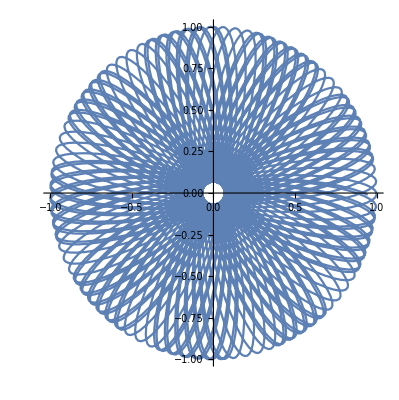

```mathematica
ParametricPlot[sol,{t,0,tmax}]
```

```mathematica
(vp-v)/Δt==-g G(h[x]+h[xp])/2
(xp-x)/Δt==(vp+v)/2
```

(-v+vp)/Δt==-1/2 g G (h[x]+h[xp])

(-x+xp)/Δt==(v+vp)/2

```mathematica
Solve[{(vp-v)/Δt==-g G h[x]+γ v/2,(xp-x)/Δt==v/2},{xp,vp}] // Simplify
```

{{xp→x+(v Δt)/2,vp→v+(v γ Δt)/2-g G Δt h[x]}}

```mathematica
eq = D[c[t],t]==1/τ(cmaxold + t/Δt(cmaxnew-cmaxold) - c[t])
```

c'[t]==(cmaxold+((cmaxnew-cmaxold) t)/Δt-c[t])/τ

```mathematica
c1 = DSolveValue[{eq,c[0]==c0},{c[t]},{t}][[1]] /. t->Δt // Simplify
```

(ⅇ^(-Δt/τ) (c0 Δt+cmaxnew (ⅇ^(Δt/τ) (Δt-τ)+τ)-cmaxold (Δt+τ-ⅇ^(Δt/τ) τ)))/Δt